```mathematica
2*8
```

16

```mathematica
6^2
```

36

```mathematica
Plus[2,3]
```

5

```mathematica
Times[2,3]
```

6

```mathematica
Times[2,Plus[2,3]]
```

10

```mathematica
Max[2,3,Plus[2,3],Times[2,6],5^6]
```

15625

```mathematica
Subtract[5,2]
```

3

```mathematica
Plus[2,2,5]
```

9

```mathematica
Subtract[5,2]
```

3

```mathematica
Divide[6,2] 6/2
```

9

```mathematica
Divide[6,2]
```

3

```mathematica
Power[2,3]
```

8

```mathematica
Min[2,3,4]
```

2

```mathematica
RandomInteger[10]
```

4

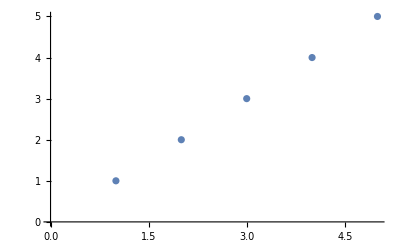

```mathematica
ListPlot[{1,2,3,4,5}]
```

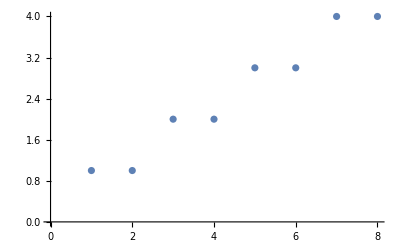

```mathematica
ListPlot[{1,1,2,2,3,3,4,4}]
```

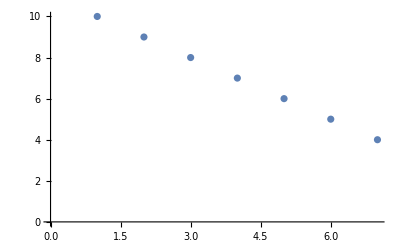

```mathematica
ListPlot[{10,9,8,7,6,5,4}]
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

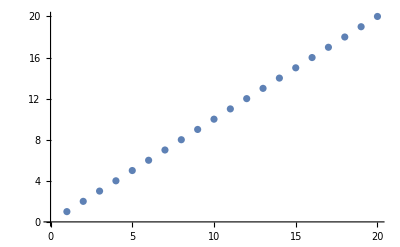

```mathematica
ListPlot[Range[20]]
```

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

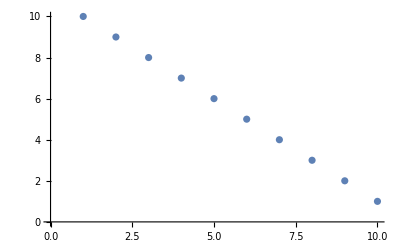

```mathematica
ListPlot[Reverse[Range[10]]]
```

```mathematica
Join[{1,2,3},{4,5,6},{7}]
```

{1,2,3,4,5,6,7}

```mathematica
Join[Range[5],Range[6]]
```

{1,2,3,4,5,1,2,3,4,5,6}

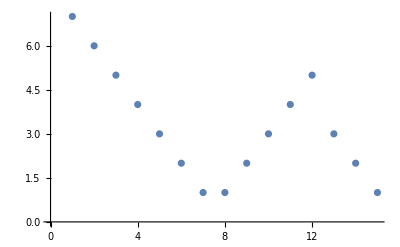

```mathematica
ListPlot[Reverse[Join[Range[3],Reverse[Range[5]],Range[7]]]]
```

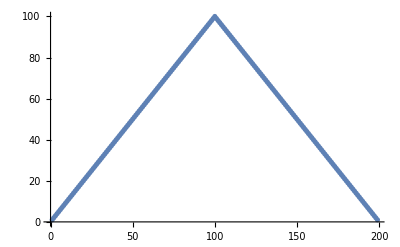

```mathematica
ListPlot[Join[Range[100],Reverse[Range[99]]]]
```

```mathematica
Range[RandomInteger[10]]
```

{1,2}

```mathematica
Divide[1,0]
```

Divide::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
1/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Range[2,7]
```

{2,3,4,5,6,7}

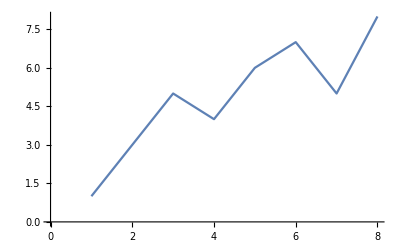

```mathematica
ListLinePlot[{1,3,5,4,6,7,5,8}]
```

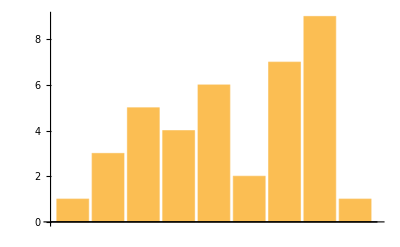

```mathematica
BarChart[{1,3,5,4,6,2,7,9,1}]
```

```mathematica
PieChart[{1,3,4,2}]
```

-Graphics-

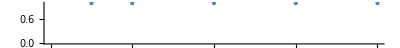

```mathematica
NumberLinePlot[{1,4,6,2,8}]
```

```mathematica
Column[{100,50,79.1}]
```

100
50
79.1

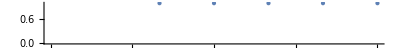
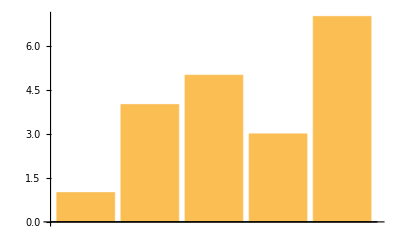
{-Graphics3D-,-Graphics-,-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
{PieChart3D[{1,5,8,9}],PieChart[Range[3]],NumberLinePlot[Range[2,6]],BarChart[{1,4,5,3,7}],BarChart3D[{1,5,2,7,9}]}
```

```mathematica
({1,2,3}+10)*3
```

{33,36,39}

```mathematica
{1,3,5}*{2,4,6}
```

{2,12,30}

```mathematica
Range[2]*Range[2]
```

{1,4}

```mathematica
Range[2]*Range[3]
```

Thread::tdlen: Objects of unequal length in {1,2} {1,2,3} cannot be combined.

{1,2} {1,2,3}

```mathematica
{1,2}*{1,2,3}
```

Thread::tdlen: Objects of unequal length in {1,2} {1,2,3} cannot be combined.

{1,2} {1,2,3}

```mathematica
Range[5]*2
Range[5]^2
```

{2,4,6,8,10}

{1,4,9,16,25}

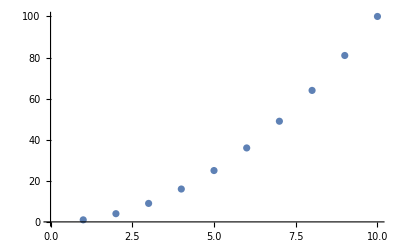

```mathematica
ListPlot[Range[10]^2]
```

```mathematica
Sort[{4,6,2,7}]
```

{2,4,6,7}

```mathematica
Length[{5,6,3,8,7,6,6,5,8}]
```

9

```mathematica
Total[{1,2,1,1}]
```

5

```mathematica
Total[Range[10]]
```

55

```mathematica
Count[{a,b,a,a,b,c, ,d},a]
```

3

```mathematica
First[{5,6,7,2,4}]
```

5

```mathematica
Last[{5,6,7,2,4}]
```

4

```mathematica
Part[{7,6,5,8,9},4]
```

8

```mathematica
First[Join[{Part[Range[10],2],{9,3}}]]
```

2

```mathematica
IntegerDigits[1984]
```

{1,9,8,4}

```mathematica
Take[IntegerDigits[1984],2]
```

{1,9}

```mathematica
Drop[Range[5],3]
```

{4,5}

```mathematica
IntegerDigits[1984,2]
```

{1,1,1,1,1,0,0,0,0,0,0}

```mathematica
IntegerDigits[1984,8]
```

{3,7,0,0}

```mathematica
IntegerDigits[1984,16]
```

{7,12,0}

```mathematica
IntegerDigits[1984,10]
```

{1,9,8,4}

```mathematica
FromDigits[{5,6,7,8}]
```

5678

```mathematica
FromDigits[{5,6}]
```

56

```mathematica
Rest[{3,4,5}]
```

{4,5}

```mathematica
Most[{3,4,5}]
```

{3,4}

```mathematica
Table[5,10]
```

{5,5,5,5,5,5,5,5,5,5}

```mathematica
Table[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

```mathematica
Table[{1,2},3]
```

{{1,2},{1,2},{1,2}}

```mathematica
Table[PieChart3D[{1,1,1}],3]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[a[n],{n,5}]
```

{a[1],a[2],a[3],a[4],a[5]}

```mathematica
Table[n+1,{n,10}]
```

{2,3,4,5,6,7,8,9,10,11}

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[Range[n],{n,5}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

```mathematica
Table[Column[Range[m]],{m,8}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8}

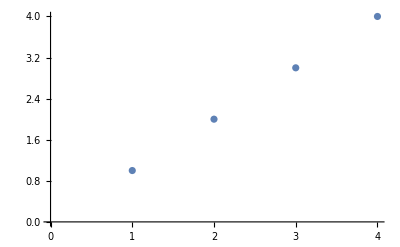
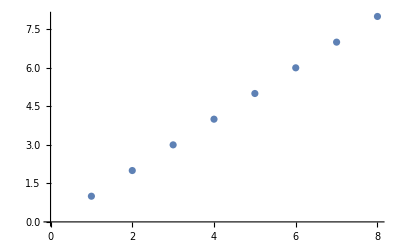
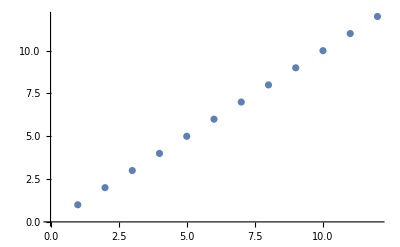

```mathematica
Table[ListPlot[Range[4*n]],{n,3}]
```

```mathematica
Table[PieChart3D[Table[1,n]],{n,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[{x,y,z},{x,3},{y,2,4},{z,3,5}]
```

{{{{1,2,3},{1,2,4},{1,2,5}},{{1,3,3},{1,3,4},{1,3,5}},{{1,4,3},{1,4,4},{1,4,5}}},{{{2,2,3},{2,2,4},{2,2,5}},{{2,3,3},{2,3,4},{2,3,5}},{{2,4,3},{2,4,4},{2,4,5}}},{{{3,2,3},{3,2,4},{3,2,5}},{{3,3,3},{3,3,4},{3,3,5}},{{3,4,3},{3,4,4},{3,4,5}}}}

```mathematica
Table[f[n],{n,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Table[f[n],{n,4,10}]
```

{f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Table[f[n],{n,4,10,2}]
```

{f[4],f[6],f[8],f[10]}

```mathematica
Range[1,2,0.1]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

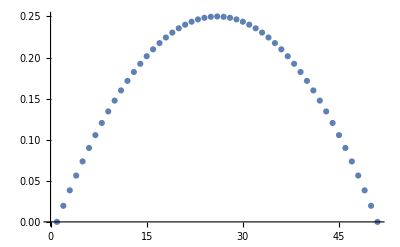

```mathematica
ListPlot[Table[x-x^2,{x,0,1,.02}]]
```

```mathematica
ListPlot[Range[0,1,.02]-Range[0,1,.02]^2]
```

-Graphics-

```mathematica
Table[RandomInteger[10],20]
```

{7,5,0,8,10,6,1,8,4,3,9,8,10,5,3,2,7,9,4,1}

```mathematica
RandomInteger[10,20]
```

{10,9,8,1,2,3,0,1,7,2,9,4,0,4,10,8,7,8,0,1}

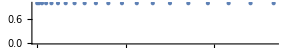

```mathematica
NumberLinePlot[Table[n^2,{n,20}]]
```

```mathematica
Range[2,20,2]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Table[n+1,{n,0,9}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

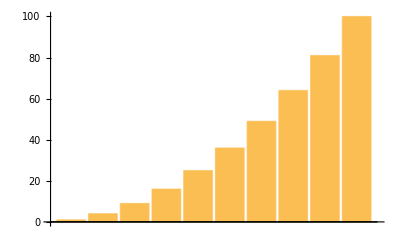

```mathematica
BarChart[Table[n^2,{n,10}]]
```

```mathematica
IntegerDigits[Table[n^2,{n,10}]]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

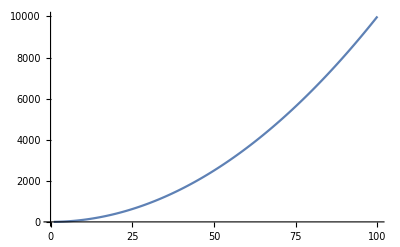

```mathematica
ListLinePlot[Table[n^2,{n,100}]]
```

```mathematica
IntegerDigits[Table[n^2,{n,100}]]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0},{1,2,1},{1,4,4},{1,6,9},{1,9,6},{2,2,5},{2,5,6},{2,8,9},{3,2,4},{3,6,1},{4,0,0},{4,4,1},{4,8,4},{5,2,9},{5,7,6},{6,2,5},{6,7,6},{7,2,9},{7,8,4},{8,4,1},{9,0,0},{9,6,1},{1,0,2,4},{1,0,8,9},{1,1,5,6},{1,2,2,5},{1,2,9,6},{1,3,6,9},{1,4,4,4},{1,5,2,1},{1,6,0,0},{1,6,8,1},{1,7,6,4},{1,8,4,9},{1,9,3,6},{2,0,2,5},{2,1,1,6},{2,2,0,9},{2,3,0,4},{2,4,0,1},{2,5,0,0},{2,6,0,1},{2,7,0,4},{2,8,0,9},{2,9,1,6},{3,0,2,5},{3,1,3,6},{3,2,4,9},{3,3,6,4},{3,4,8,1},{3,6,0,0},{3,7,2,1},{3,8,4,4},{3,9,6,9},{4,0,9,6},{4,2,2,5},{4,3,5,6},{4,4,8,9},{4,6,2,4},{4,7,6,1},{4,9,0,0},{5,0,4,1},{5,1,8,4},{5,3,2,9},{5,4,7,6},{5,6,2,5},{5,7,7,6},{5,9,2,9},{6,0,8,4},{6,2,4,1},{6,4,0,0},{6,5,6,1},{6,7,2,4},{6,8,8,9},{7,0,5,6},{7,2,2,5},{7,3,9,6},{7,5,6,9},{7,7,4,4},{7,9,2,1},{8,1,0,0},{8,2,8,1},{8,4,6,4},{8,6,4,9},{8,8,3,6},{9,0,2,5},{9,2,1,6},{9,4,0,9},{9,6,0,4},{9,8,0,1},{1,0,0,0,0}}

```mathematica
Red
```

RGBColor[1, 0, 0]

```mathematica
Blue
```

RGBColor[0, 0, 1]

```mathematica
{Red,Blue,Green,Yellow,White,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 1, 0],GrayLevel[1],GrayLevel[0]}

```mathematica
ColorNegate[Red]
```

RGBColor[0., 1., 1.]

```mathematica
Blend[{Red,Blue}]
```

RGBColor[Rational[1, 2], 0, Rational[1, 2]]

```mathematica
Blend[{Red,Yellow,Green}]
```

RGBColor[Rational[2, 3], Rational[2, 3], 0]

```mathematica
Blend[{Red,Yellow},1/3]
Blend[{Red,Yellow}]
```

RGBColor[1, Rational[1, 3], 0]

RGBColor[1, Rational[1, 2], 0]

```mathematica
RGBColor[1,0,0]
```

RGBColor[1, 0, 0]

```mathematica
RGBColor[1,1,0]
```

RGBColor[1, 1, 0]

```mathematica
RGBColor[1,1,1]
```

RGBColor[1, 1, 1]

```mathematica
RGBColor[0,0,0]
```

RGBColor[0, 0, 0]

```mathematica
Table[RGBColor[1,g,0],{g,0,1,0.05}]
```

{RGBColor[1, 0., 0],RGBColor[1, 0.05, 0],RGBColor[1, 0.1, 0],RGBColor[1, 0.15000000000000002, 0],RGBColor[1, 0.2, 0],RGBColor[1, 0.25, 0],RGBColor[1, 0.30000000000000004, 0],RGBColor[1, 0.35000000000000003, 0],RGBColor[1, 0.4, 0],RGBColor[1, 0.45, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.55, 0],RGBColor[1, 0.6000000000000001, 0],RGBColor[1, 0.65, 0],RGBColor[1, 0.7000000000000001, 0],RGBColor[1, 0.75, 0],RGBColor[1, 0.8, 0],RGBColor[1, 0.8500000000000001, 0],RGBColor[1, 0.9, 0],RGBColor[1, 0.9500000000000001, 0],RGBColor[1, 1., 0]}

```mathematica
Hue[0.5]
```

Hue[0.5]

```mathematica
Table[Hue[g],{g,0,1,0.05}]
```

{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}

```mathematica
RandomColor[]
```

RGBColor[0.8007024524276389, 0.828812806502017, 0.7964347605754245]

```mathematica
Table[RandomColor[],30]
```

{RGBColor[0.7879545055781143, 0.174835326114128, 0.7422843970135256],RGBColor[0.12456606626855393, 0.6614288037703739, 0.026964398780779497],RGBColor[0.7814885371047211, 0.4034124455320911, 0.9954769049255825],RGBColor[0.5018997546580595, 0.9531721352874982, 0.6303820670292939],RGBColor[0.22615737568357264, 0.7909797476277933, 0.026642253796435478],RGBColor[0.28893940202980484, 0.9323367598485448, 0.7490678534351174],RGBColor[0.5299085173390108, 0.6336675580062019, 0.7073150830483728],RGBColor[0.425735851732187, 0.9777848605113129, 0.15395072169059354],RGBColor[0.8636071809139017, 0.8728690723846435, 0.285929013949892],RGBColor[0.17597769484836778, 0.5469293150760657, 0.7416706779847226],RGBColor[0.5831644711385147, 0.22463894782770577, 0.7604324846971089],RGBColor[0.8617745902078895, 0.16214454186707616, 0.8521886710061002],RGBColor[0.9885522668572273, 0.11409887160079646, 0.6959569400344965],RGBColor[0.8275608921335758, 0.3851772211985187, 0.06677295290881147],RGBColor[0.2338410290821109, 0.4338700026523432, 0.06724421007635328],RGBColor[0.5609284130112087, 0.5570028876201456, 0.1450036380207298],RGBColor[0.6033622675509611, 0.09976187729774555, 0.7634504737684618],RGBColor[0.8928826560778171, 0.18879297467233735, 0.8529665582418207],RGBColor[0.5704621597704835, 0.4372705701576163, 0.4071995880448833],RGBColor[0.17908402882005658, 0.552526400407549, 0.7898845674173194],RGBColor[0.3205272305406941, 0.33506055651904987, 0.4203386901368278],RGBColor[0.38297421065009996, 0.9923765205233634, 0.797716436410838],RGBColor[0.730025112710933, 0.3047206512802134, 0.9916380031884531],RGBColor[0.5876808382064744, 0.17634615844656665, 0.6336054668489524],RGBColor[0.1469052493450398, 0.5428986568953174, 0.08188222942729961],RGBColor[0.03079707908940743, 0.027583104470554565, 0.11193684552579031],RGBColor[0.20081567005544732, 0.386075730066082, 0.10960553803171269],RGBColor[0.34844453561730204, 0.46727599618844295, 0.5989301972761472],RGBColor[0.17723866886408568, 0.8358751476288844, 0.41252366414526387],RGBColor[0.3517777000371387, 0.5131660488622285, 0.33979672605468614]}

```mathematica
Blend[Table[RandomColor[],20]]
```

RGBColor[0.5349637346248071, 0.4496965688823211, 0.5415012360381631]

```mathematica
Style[1000,Red]
```

1000

```mathematica
Table[Style[RandomInteger[1000],RandomColor[]],30]
```

{21,432,787,1,848,876,692,493,100,227,146,694,248,567,339,534,296,854,173,589,391,788,989,356,402,939,836,541,643,582}

```mathematica
Style[x,30,Red]
```

x

```mathematica
Table[Style[100,n],{n,20}]
```

{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}

```mathematica
Table[Style[x,RandomColor[],RandomInteger[30]],25]
```

{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}

```mathematica
Problem:using Part and RandomInteger to make a list which include 100elements ,and every element is used by red ,yellow or green to display.
```